```mathematica
f[a_,E_]:=(Cos[a]^2+Exp[-E]*Sin[a]^2)/(Cos[a]^4+Exp[-E]*Sin[a]^4)
```

0.591231

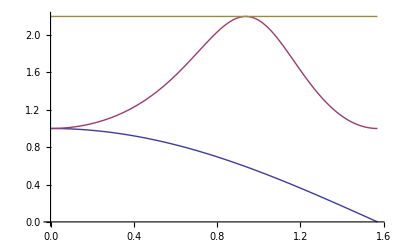

```mathematica
e=.138*9;Cos[ArcTan[Exp[e/4]]]
Plot[{Cos[a],f[a,e],1+Cosh[e/2]},{a,0,Pi/2}]
```

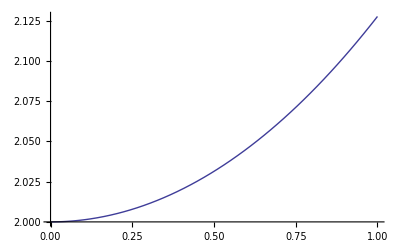

```mathematica
Plot[1/2 ⅇ^(-tE/2) (1+ⅇ^(tE/2))^2,{tE,0,1}]
```

```mathematica
Simplify[f[ArcTan[Exp[tE/4]],tE]]
```

1/2 ⅇ^(-tE/2) (1+ⅇ^(tE/2))^2

```mathematica
Expand[1/2 ⅇ^(-tE/2) (1+ⅇ^(tE/2))^2]
```

1+ⅇ^(-tE/2)/2+ⅇ^(tE/2)/2

```mathematica
1+Cosh[-tE/2]
```

1+Cosh[tE/2]

```mathematica
Simplify[D[f[a,e],a]*(Cos[a]^4+e Sin[a]^4)^2]
```

((Cos[a]^4+1.242 Sin[a]^4)^2 (2.57761 Cos[a]^5 Sin[a]-0.74443 Cos[a] Sin[a]^5))/((Cos[a]^4+0.288806 Sin[a]^4)^2)

```mathematica
Solve[Cos[a]^4-e Sin[a]^4==0,a]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{a→-ArcCos[-√(-(√e)/(-1+e)+e/(-1+e))]},{a→ArcCos[-√(-(√e)/(-1+e)+e/(-1+e))]},{a→-ArcCos[√(-(√e)/(-1+e)+e/(-1+e))]},{a→ArcCos[√(-(√e)/(-1+e)+e/(-1+e))]},{a→-ArcCos[-√((√e)/(-1+e)+e/(-1+e))]},{a→ArcCos[-√((√e)/(-1+e)+e/(-1+e))]},{a→-ArcCos[√((√e)/(-1+e)+e/(-1+e))]},{a→ArcCos[√((√e)/(-1+e)+e/(-1+e))]}}